# Nucleosynthesis

## Environment

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],CellContext->Notebook];
```

## Boxes

```mathematica
MakeBoxes[age, StandardForm]:=SubscriptBox["t", "0"]; 
MakeExpression[SubscriptBox["t", "0"], StandardForm]:=MakeExpression["age", StandardForm]; 
MakeBoxes[ageInConformalTime, StandardForm]:=SubscriptBox["η", "0"]; 
MakeExpression[SubscriptBox["η", "0"], StandardForm]:=MakeExpression["ageInConformalTime", StandardForm]; 
MakeBoxes[baryonDensity, StandardForm]:=SubscriptBox["ρ", "B"]; 
MakeExpression[SubscriptBox["ρ", "B"], StandardForm]:=MakeExpression["baryonDensity", StandardForm]; 
MakeBoxes[boltzmannConstant, StandardForm]:=SubscriptBox["k", "B"]; 
MakeExpression[SubscriptBox["k", "B"], StandardForm]:=MakeExpression["boltzmannConstant",StandardForm]; 
MakeBoxes[baryonToPhotonNumberRatio, StandardForm]:=SuperscriptBox["η", "0"]; 
MakeExpression[SuperscriptBox["η", "0"], StandardForm]:=MakeExpression["baryonToPhotonNumberRatio", StandardForm]; 
MakeBoxes[currentTemperature, StandardForm]:=SubscriptBox["T", "0"]; 
MakeExpression[SubscriptBox["T", "0"], StandardForm]:=MakeExpression["currentTemperature",StandardForm]; 
MakeBoxes[deuteriumBindingEnergy, StandardForm]:=SubscriptBox["B", "D"]; 
MakeExpression[SubscriptBox["B", "D"], StandardForm] :=MakeExpression["deuteriumBindingEnergy", StandardForm]; 
MakeBoxes[deuteriumMass, StandardForm]:=SubscriptBox["m", "D"]; 
MakeExpression[SubscriptBox["m", "D"], StandardForm]:=MakeExpression["deuteriumMass", StandardForm]; 
MakeBoxes[distanceLastScatteringSurface, StandardForm]:=SubscriptBox["D", "LSS"]; 
MakeExpression[SubscriptBox["D", "LSS"], StandardForm] :=MakeExpression["distanceLastScatteringSurface", StandardForm]; 
MakeBoxes[electronDensity, StandardForm]:=SubscriptBox["n", "e"]; 
MakeExpression[SubscriptBox["n", "e"], StandardForm]:=MakeExpression["electronDensity",StandardForm]; 
MakeBoxes[equilibriumNumberDensity, StandardForm]:=SubscriptBox["n", "(0)"]; 
MakeExpression[SubscriptBox["n", "(0)"], StandardForm]:=MakeExpression["equilibriumNumberDensity",StandardForm]; 
MakeBoxes[freeElectronFraction, StandardForm]:=SubscriptBox["X", "e"]; 
MakeExpression[SubscriptBox["X", "e"], StandardForm]:=MakeExpression["freeElectronFraction",StandardForm]; 
MakeBoxes[flatCurvature, StandardForm]:=SubscriptBox["k", "Z"]; 
MakeExpression[SubscriptBox["k", "Z"], StandardForm]:=MakeExpression["flatCurvature", StandardForm]; 
MakeBoxes[hydrogenAbundance, StandardForm]:=SubscriptBox["A", "H"]; 
MakeExpression[SubscriptBox["A", "H"], StandardForm]:=MakeExpression["hydrogenAbundance",StandardForm]; 
MakeBoxes[hydrogenMass, StandardForm]:=SubscriptBox["m", "H"]; 
MakeExpression[SubscriptBox["m", "H"], StandardForm]:=MakeExpression["hydrogenMass", StandardForm]; 
MakeBoxes[heliumAbundance, StandardForm]:=SubscriptBox["A", "He"]; 
MakeExpression[SubscriptBox["A", "He"], StandardForm]:=MakeExpression["heliumAbundance",StandardForm]; 
MakeBoxes[heliumMass, StandardForm]:=SubscriptBox["m", "He"]; 
MakeExpression[SubscriptBox["m", "He"], StandardForm]:=MakeExpression["heliumMass", StandardForm]; 
MakeBoxes[hyperspherical, StandardForm]:=SubscriptBox["S", "k"]; 
MakeExpression[SubscriptBox["S", "k"], StandardForm]:=MakeExpression["hyperspherical", StandardForm]; 
MakeBoxes[hubbleConstant, StandardForm]:=SubscriptBox["H", "0"]; 
MakeExpression[SubscriptBox["H", "0"], StandardForm]:=MakeExpression["hubbleConstant", StandardForm]; 
MakeBoxes[mevFromKg, StandardForm]:=SubscriptBox["MeV", "kg"]; 
MakeExpression[SubscriptBox["MeV", "kg"], StandardForm]:=MakeExpression["mevFromKg", StandardForm]; 
MakeBoxes[negativeCurvature, StandardForm]:=SubscriptBox["k", "N"]; 
MakeExpression[SubscriptBox["k", "N"], StandardForm]:=MakeExpression["negativeCurvature", StandardForm]; 
MakeBoxes[neutronMass, StandardForm]:=SubscriptBox["m", "n"]; 
MakeExpression[SubscriptBox["m", "n"], StandardForm]:=MakeExpression["neutronMass", StandardForm]; 
MakeBoxes[particleHorizon, StandardForm]:=SubscriptBox["H", "p"]; 
MakeExpression[SubscriptBox["H", "p"], StandardForm]:=MakeExpression["particleHorizon",StandardForm]; 
MakeBoxes[photonDensity, StandardForm]:=SubscriptBox["ρ", "γ"]; 
MakeExpression[SubscriptBox["ρ", "γ"], StandardForm]:=MakeExpression["photonDensity",StandardForm]; 
MakeBoxes[positiveCurvature, StandardForm]:=SubscriptBox["k", "P"]; 
MakeExpression[SubscriptBox["k", "P"], StandardForm]:=MakeExpression["positiveCurvature", StandardForm]; 
MakeBoxes[protonMass, StandardForm]:=SubscriptBox["m", "p"]; 
MakeExpression[SubscriptBox["m", "p"], StandardForm]:=MakeExpression["protonMass", StandardForm]; 
MakeBoxes[randomConstant, StandardForm]:=SubscriptBox["a", "B"]; 
MakeExpression[SubscriptBox["a", "B"], StandardForm]:=MakeExpression["randomConstant", StandardForm]; 
MakeBoxes[redshiftFromConformalTime, StandardForm]:=SubscriptBox["z", "η"]; 
MakeExpression[SubscriptBox["z", "η"], StandardForm]:=MakeExpression["redshiftFromConformalTime",StandardForm]; 
MakeBoxes[redshiftOfRecombination, StandardForm]:=SubscriptBox["z", "*"]; 
MakeExpression[SubscriptBox["z", "*"], StandardForm]:=MakeExpression["redshiftOfRecombination", StandardForm]; MakeBoxes[scaleFactorFromRedshift, StandardForm]:=SubscriptBox["a", "z"]; 
MakeExpression[SubscriptBox["a", "z"], StandardForm]:=MakeExpression["scaleFactorFromRedshift", StandardForm]; 
MakeBoxes[scaleFactorFromTime, StandardForm]:=SubscriptBox["a", "t"]; 
MakeExpression[SubscriptBox["a", "t"], StandardForm]:=MakeExpression["scaleFactorFromTime",StandardForm]; 
MakeBoxes[scatterRate, StandardForm]:=OverscriptBox["τ", "."]; 
MakeExpression[OverscriptBox["τ", "."], StandardForm]:=MakeExpression["scatterRate", StandardForm]; 
MakeBoxes[soundHorizon, StandardForm]:=SubscriptBox["s", "*"]; 
MakeExpression[SubscriptBox["s", "*"], StandardForm]:=MakeExpression["soundHorizon", StandardForm]; 
MakeBoxes[speedOfLight, StandardForm]:=SubscriptBox["c", "3"]; 
MakeExpression[SubscriptBox["c", "3"], StandardForm]:=MakeExpression["speedOfLight", StandardForm]; 
MakeBoxes[thetaPrime, StandardForm]:=SuperscriptBox["θ", "′"]; 
MakeExpression[Superscript["θ", "′"], StandardForm]:=MakeExpression["thetaPrime", StandardForm]; 
MakeBoxes[thomsonScatteringCrossSection, StandardForm]:=SubscriptBox["σ", "T"]; 
MakeExpression[SubscriptBox["σ", "T"], StandardForm] :=MakeExpression["thomsonScatteringCrossSection", StandardForm]; 
MakeBoxes[timeFromConformalTime, StandardForm]:=SubscriptBox["t", "η"]; 
MakeExpression[SubscriptBox["t", "η"], StandardForm]:=MakeExpression["timeFromConformalTime", StandardForm]; 
MakeBoxes[timeFromRedshift, StandardForm]:=SubscriptBox["t", "z"]; 
MakeExpression[SubscriptBox["t", "z"], StandardForm]:=MakeExpression["timeFromRedshift",StandardForm]; 
MakeBoxes[timeFromTemperature, StandardForm]:=SubscriptBox["t", "K"]; 
MakeExpression[SubscriptBox["t", "K"], StandardForm]:=MakeExpression["timeFromTemperature",StandardForm]; 
MakeBoxes[universeAcceleration, StandardForm]:=SubscriptBox["A", "3"]; 
MakeExpression[SubscriptBox["A", "3"], StandardForm]:=MakeExpression["universeAcceleration",StandardForm]; 

MakeBoxes[ageOfCMB, StandardForm]:=SubscriptBox["t", "CMB"]; 
MakeExpression[SubscriptBox["t", "CMB"], StandardForm]:=MakeExpression["ageOfCMB", StandardForm]; 
MakeBoxes[deuteriumEquilibriumNumberDensity, StandardForm]:=SubsuperscriptBox["n","D","0"]; 
MakeExpression[SubsuperscriptBox["n","D","0"], StandardForm]:=MakeExpression["deuteriumEquilibriumNumberDensity",StandardForm]; 
MakeBoxes[scaleFactorFromTime, StandardForm]:=SubscriptBox["a", "t"]; 
MakeExpression[SubscriptBox["a", "t"], StandardForm]:=MakeExpression["scaleFactorFromTime",StandardForm]; 
MakeBoxes[temperatureFromTime, StandardForm]:=SubscriptBox["T", "t"]; 
MakeExpression[SubscriptBox["T", "t"], StandardForm]:=MakeExpression["temperatureFromTime",StandardForm]; 
MakeBoxes[energyFromTime, StandardForm]:=SubscriptBox["E", "t"]; 
MakeExpression[SubscriptBox["E", "t"], StandardForm]:=MakeExpression["energyFromTime",StandardForm]; 
MakeBoxes[neutronsToTotalNucliei, StandardForm]:=SubscriptBox["X", "n"]; 
MakeExpression[SubscriptBox["X", "n"], StandardForm]:=MakeExpression["neutronsToTotalNucliei",StandardForm]; 
MakeBoxes[numberOfNeutrons, StandardForm]:=SubscriptBox["n", "n"]; 
MakeExpression[SubscriptBox["n", "n"], StandardForm]:=MakeExpression["numberOfNeutrons",StandardForm]; 
MakeBoxes[numberOfprotons, StandardForm]:=SubscriptBox["n", "p"]; 
MakeExpression[SubscriptBox["n", "p"], StandardForm]:=MakeExpression["numberOfprotons",StandardForm]; 
MakeBoxes[speciesDegeneracy, StandardForm]:=SubscriptBox["g", "i"]; 
MakeExpression[SubscriptBox["g", "i"], StandardForm]:=MakeExpression["speciesDegeneracy",StandardForm]; 
MakeBoxes[neutronEquilibriumNumberDensity, StandardForm]:=SubsuperscriptBox["n","n","0"]; 
MakeExpression[SubsuperscriptBox["n","n","0"], StandardForm]:=MakeExpression["neutronEquilibriumNumberDensity",StandardForm]; 
MakeBoxes[speciesEquilibriumNumberDensity, StandardForm]:=SubsuperscriptBox["n","i","0"]; 
MakeExpression[SubsuperscriptBox["n","i","0"], StandardForm]:=MakeExpression["speciesEquilibriumNumberDensity",StandardForm]; 
MakeBoxes[protonEquilibriumNumberDensity, StandardForm]:=SubsuperscriptBox["n","p","0"]; 
MakeExpression[SubsuperscriptBox["n","p","0"], StandardForm]:=MakeExpression["protonEquilibriumNumberDensity",StandardForm]; 
MakeBoxes[photonDegenercy, StandardForm]:=SubscriptBox["g", "γ"]; 
MakeExpression[SubscriptBox["g", "γ"], StandardForm]:=MakeExpression["photonDegenercy",StandardForm]; 
MakeBoxes[neutronDegenercy, StandardForm]:=SubscriptBox["g", "n"]; 
MakeExpression[SubscriptBox["g", "n"], StandardForm]:=MakeExpression["neutronDegenercy",StandardForm]; 
MakeBoxes[protonDegenercy, StandardForm]:=SubscriptBox["g", "p"]; 
MakeExpression[SubscriptBox["g", "p"], StandardForm]:=MakeExpression["protonDegenercy",StandardForm]; 
MakeBoxes[deuteriumDegenercy, StandardForm]:=SubscriptBox["g", "D"]; 
MakeExpression[SubscriptBox["g", "D"], StandardForm]:=MakeExpression["deuteriumDegenercy",StandardForm]; 
MakeBoxes[speciesMass, StandardForm]:=SubscriptBox["m", "i"]; 
MakeExpression[SubscriptBox["m", "i"], StandardForm]:=MakeExpression["speciesMass",StandardForm]; 
MakeBoxes[speciesEnergy, StandardForm]:=SubscriptBox["E", "i"]; 
MakeExpression[SubscriptBox["E", "i"], StandardForm]:=MakeExpression["speciesEnergy",StandardForm]; 
MakeBoxes[speciesNumberDensity, StandardForm]:=SubscriptBox["n", "i"]; 
MakeExpression[SubscriptBox["n", "i"], StandardForm]:=MakeExpression["speciesNumberDensity",StandardForm]; 
MakeBoxes[speciesChemicalPotential, StandardForm]:=SubscriptBox["μ", "i"]; 
MakeExpression[SubscriptBox["μ", "i"], StandardForm]:=MakeExpression["speciesChemicalPotential",StandardForm]; 
MakeBoxes[TMeV, StandardForm]:=SubscriptBox["T", "MeV"]; 
MakeExpression[SubscriptBox["T", "MeV"], StandardForm]:=MakeExpression["TMeV",StandardForm]; 
MakeBoxes[neutronRatioAtEqulibrium, StandardForm]:=SubscriptBox["X", "e,EQ"]; 
MakeExpression[SubscriptBox["X", "e,EQ"], StandardForm]:=MakeExpression["neutronRatioAtEqulibrium",StandardForm]; 
MakeBoxes[neutronProtonConversionRate, StandardForm]:=SubscriptBox["λ", "np"]; 
MakeExpression[SubscriptBox["λ", "np"], StandardForm]:=MakeExpression["neutronProtonConversionRate",StandardForm]; 
MakeBoxes[neutronLifetime, StandardForm]:=SubscriptBox["τ", "n"]; 
MakeExpression[SubscriptBox["τ", "n"],StandardForm]:=MakeExpression["neutronLifetime",StandardForm]; 
MakeBoxes[evolutionParameter, StandardForm]:=SubscriptBox["x", "t"]; 
MakeExpression[SubscriptBox["x", "t"],StandardForm]:=MakeExpression["evolutionParameter",StandardForm]; 
MakeBoxes[xPrime, StandardForm]:=SuperscriptBox["x", "′"]; 
MakeExpression[SuperscriptBox["x", "′"],StandardForm]:=MakeExpression["xPrime",StandardForm]; 
MakeBoxes[timeFromEvolutionParameter, StandardForm]:=SubscriptBox["t", "x"]; 
MakeExpression[SubscriptBox["t", "x"],StandardForm]:=MakeExpression["timeFromEvolutionParameter",StandardForm];
```

## Clear Variables

```mathematica
ClearAll[G,ℏ,Subscript[k, B],Subscript[c, 3],Subscript[A, 3],Subscript[t, 0],Subscript[t, CMB],Subscript[η, 0],h,Subscript[H, 0],Subscript[T, 0],Subscript[τ, n],Subscript[m, p],Subscript[m, n],Subscript[m, H],Subscript[m, D],Subscript[m, He]];
ClearAll[Subscript[n, D]^0,Subscript[n, p]^0,Subscript[n, n]^0,Subscript[λ, np],Subscript[X, n]]
```

## Units

```mathematica
s=1;
m=1;
kg=1;
K=1;
cm=0.01 m;
g=0.001 kg;
J=(kg m^2)/s^2;
MeV=1.1604525×10^10 K;
km=1000 m;
yr=60 60 24 365.25s;
kyr=1000 yr;
Myr=1000 kyr;
Gyr=1000 Myr;
pc=3.08567758 10^13 km;
kpc=1000 pc;
Mpc=1000 kpc;
Gpc=1000 Mpc;
```

## Functions

### Scale Factor from Coordinate Time

```mathematica
Subscript[a, t][t_]:=t^2/Subscript[t, 0]^2
```

### Temperature From Coordinate Time (K)

```mathematica
Subscript[T, t][t_]:=Subscript[T, 0]/(Subscript[a, t][t])
```

### Coordinate Time from Temperature (s)

```mathematica
Subscript[t, K][T_]:=√((Subscript[T, 0] Subscript[t, 0]^2)/T)
```

### Energy from rest mass energy and kinetic energy.

```mathematica
energy=Subscript[E, i]^2==Subscript[m, i]^2 c^4+p^2 c^2;
energy=Equal@@FullSimplify[Solve[energy,Subscript[E, i]]/.p->Subscript[m, i] v,Assumptions->Subscript[m, i]≥0]⟦2,1⟧;
energy=(Normal[Series[energy,{v,0,2}]]/.v->p/Subscript[m, i])[[2]]
```

(c p^2)/(2 √(c^2) m_i)+c √(c^2) m_i

### Evolution Parameter

```mathematica
Subscript[x, t][t_]:=(c^2 t^2 (Subscript[m, n]-Subscript[m, p]))/(Subscript[k, B] Subscript[t, 0]^2 Subscript[T, 0])/.c->Subscript[c, 3]
```

```mathematica
Subscript[t, x][x_]:=√((x Subscript[k, B] Subscript[T, 0] Subscript[t, 0]^2)/((Subscript[m, n]-Subscript[m, p]) c^2))/.c->Subscript[c, 3]
```

### Number Density for a particle species.

```mathematica
Subscript[n, i]=Hold[Subscript[g, i] ⅇ^(Subscript[μ, i]/(Subscript[k, B] T)) (∫_0^∞ p^2/(2 π ℏ)^3 ⅇ^(-Subscript[E, i]/(Subscript[k, B] T))ⅆp) (∫_0^π Sin[θ]ⅆθ) ∫_0^(2 π) 1ⅆϕ];
```

### Equilibrium Number Density (μ_i→0)

```mathematica
Subscript[n, i]^0=Simplify[ReleaseHold[Subscript[n, i]/.Subscript[μ, i]->0/.Subscript[E, i]->energy],Assumptions->{Subscript[k, B]>0,Subscript[m, i]>0,T>0,c>0}]
```

(ⅇ^(-(c^2 m_i)/(k_B T)) g_i (k_B m_i T)^(3/2))/(2 √2 π^(3/2) ℏ^3)

```mathematica
(Subscript[n, D]^0)[T_]=Simplify[Subscript[n, i]^0/.Subscript[m, i]->Subscript[m, D]/.Subscript[g, i]->Subscript[g, D]/.c->Subscript[c, 3]];
(Subscript[n, p]^0)[T_]=Simplify[Subscript[n, i]^0/.Subscript[m, i]->Subscript[m, p]/.Subscript[g, i]->Subscript[g, p]/.c->Subscript[c, 3]]
(Subscript[n, n]^0)[T_]=Simplify[Subscript[n, i]^0/.Subscript[m, i]->Subscript[m, n]/.Subscript[g, i]->Subscript[g, n]/.c->Subscript[c, 3]];
```

(ⅇ^(-(m_p c_3^2)/(k_B T)) g_p (k_B m_p T)^(3/2))/(2 √2 π^(3/2) ℏ^3)

```mathematica
Subscript[X, e,EQ][T_]=1/(1+((Subscript[n, p]^0)[T])/((Subscript[n, n]^0)[T]));
```

## Constants

```mathematica
G=(6.67408 m^3)/(10^11 kg s^2);
ℏ=(6.62607004 J)/(2 π 10^34 s);
Subscript[k, B]=(1.38064852 J)/(10^23 K);
Subscript[c, 3]=(2.99792458 10^8 m)/s;
Subscript[A, 3]=(4.38693 km)/(10^14 s^2);
Subscript[t, 0]=8.57697 10^17 s;
Subscript[t, CMB]=2.4714 10^16 s;
η^0=1.5/10^8;
h=(2 Mpc)/((100 Subscript[t, 0]) km);
Subscript[H, 0]=(h 100 km)/(s Mpc);
Subscript[T, 0]=2.7255 K;
Subscript[τ, n]=886.7 s;
Q=1.293 MeV;
```

### Particle Masses

```mathematica
Subscript[m, p]=(1.6726219 kg)/10^27;
Subscript[m, n]=(1.6749274 kg)/10^27;
Subscript[m, H]=(1.6735575 kg)/10^27;
Subscript[m, D]=(3.3435837 kg)/10^27;
Subscript[m, He]=(6.6464764 kg)/10^27;
```

### Species Degeneracy

```mathematica
Subscript[g, γ]=2;
Subscript[g, p]=2;
Subscript[g, n]=2;
Subscript[g, D]=3;
```

## Neutron to Proton Abundance in Equilibrium

```mathematica
Axis1MeV={{Automatic,Automatic},{{{Subscript[t, K][1 MeV],"1"},{Subscript[t, K][0.9 MeV],Null},{Subscript[t, K][0.8 MeV],Null},{Subscript[t, K][0.7 MeV],Null},{Subscript[t, K][0.6 MeV],Null},{Subscript[t, K][0.5 MeV],Null},{Subscript[t, K][0.4 MeV],Null},{Subscript[t, K][0.3 MeV],Null},{Subscript[t, K][0.2 MeV],Null},{Subscript[t, K][0.1 MeV],"0.1"},{Subscript[t, K][0.09 MeV],Null},{Subscript[t, K][0.08 MeV],Null},{Subscript[t, K][0.07 MeV],Null},{Subscript[t, K][0.06 MeV],Null},{Subscript[t, K][0.05 MeV],Null},{Subscript[t, K][0.04 MeV],Null},{Subscript[t, K][0.03 MeV],Null}},None}};
```

```mathematica
Axis100MeV={{Automatic,Automatic},{{{Subscript[t, K][1000 MeV],"1K"},{Subscript[t, K][900 MeV],Null},{Subscript[t, K][800 MeV],Null},{Subscript[t, K][700 MeV],Null},{Subscript[t, K][600 MeV],Null},{Subscript[t, K][500 MeV],Null},{Subscript[t, K][400 MeV],Null},{Subscript[t, K][300 MeV],Null},{Subscript[t, K][200 MeV],Null},{Subscript[t, K][100 MeV],"100"},{Subscript[t, K][90 MeV],Null},{Subscript[t, K][80 MeV],Null},{Subscript[t, K][70 MeV],Null},{Subscript[t, K][60 MeV],Null},{Subscript[t, K][50 MeV],Null},{Subscript[t, K][40 MeV],Null},{Subscript[t, K][30 MeV],Null},{Subscript[t, K][20 MeV],Null},{Subscript[t, K][10 MeV],"10"},{Subscript[t, K][9 MeV],Null},{Subscript[t, K][8 MeV],Null},{Subscript[t, K][7 MeV],Null},{Subscript[t, K][6 MeV],Null},{Subscript[t, K][5 MeV],Null},{Subscript[t, K][4 MeV],Null},{Subscript[t, K][3 MeV],Null},{Subscript[t, K][2 MeV],Null},{Subscript[t, K][1 MeV],"1"}},None}};
```

### Neutron Fraction with x

```mathematica
ClearAll[Subscript[X, n],x,neutronFraction]
Subscript[λ, np][x_]:=Rationalize[(255(12+6 x+x^2))/(Subscript[τ, n] x^5),0];
H[x_]:=Rationalize[2/Subscript[t, x][x],0];
equation=Subscript[X, n]'[x]==(Subscript[λ, np][x] /(x H[x]))((1-Subscript[X, n][x]) ⅇ^-x-Subscript[X, n][x]);
initialConditions=Rationalize[Subscript[X, n][Subscript[x, t][Subscript[t, K][2 MeV]]]==Subscript[X, e,EQ][2 MeV],0];
Subscript[X, n][x_]=Subscript[X, n][x]/.NDSolve[{equation,initialConditions},Subscript[X, n][x],{x,Subscript[x, t][Subscript[t, K][2 MeV]],Subscript[x, t][Subscript[t, K][0.01 MeV]]},WorkingPrecision->30,Method->"StiffnessSwitching"];
```

### Proton Anti - Proton Pair Creation

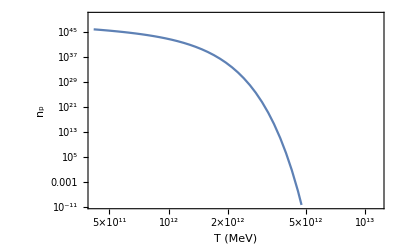

```mathematica
LogLogPlot[{(Subscript[n, p]^0)[Subscript[T, t][t]]},{t,Subscript[t, K][1000 MeV],Subscript[t, K][1 MeV]},PlotRange->{1/(3×10^10),10^50},Frame->True,FrameLabel->{"T (MeV)","n_p"},LabelStyle->{FontSize->13},FrameStyle->Thickness[0.004],FrameTicks->Axis100MeV]
```

```mathematica
delta=10^10
```

10000000000

```mathematica
(Subscript[n, p]^0)[Subscript[T, t][10^12]]
(Subscript[n, n]^0)[Subscript[T, t][10^12]]
```

4.7258×10^42

4.70026×10^42

```mathematica
(((Subscript[n, p]^0)[Subscript[T, t][10^12]]-(Subscript[n, p]^0)[Subscript[T, t][10^12+10^10]])*(Subscript[a, t][10^12])^3)
```

1.54052×10^6

```mathematica
Sum[protonEquilibriumNumberDensity[temperatureFromTime[t]] - protonEquilibriumNumberDensity[
    temperatureFromTime[t + delta]], {t, 10^10, 10^14}]
```

∑_(t=10000000000)^100000000000000 (1.07876×10^81 ⅇ^(-5.43053×10^-24 t^2) (1/t^2)^(3/2)-1.07876×10^81 ⅇ^(-5.43053×10^-24 (10000000000+t)^2) (1/(10000000000+t)^2)^(3/2))

### Deuterium Fraction

```mathematica
deuteriumFraction[T_]=((Subscript[n, D]^0)[T])/((Subscript[n, n]^0)[T] (Subscript[n, p]^0)[T])
```

(1.11343×10^-26 ⅇ^(2.58147×10^10/T))/T^(3/2)

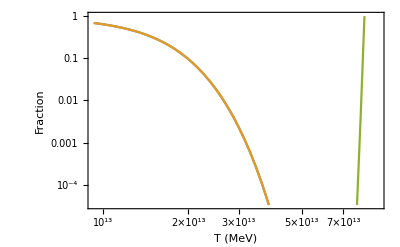

```mathematica
LogLogPlot[{2 Subscript[X, e,EQ][Subscript[T, t][t]],2 Subscript[X, n][Subscript[x, t][t]],deuteriumFraction[Subscript[T, t][t]]},{t,Subscript[t, K][2.0 MeV],Subscript[t, K][0.02 MeV]},PlotRange->{1/(3×10^4),1},Frame->True,FrameLabel->{"T (MeV)","Fraction"},LabelStyle->{FontSize->13},FrameStyle->Thickness[0.004],FrameTicks->Axis1MeV]
```

```mathematica
tnuc[T_]=(ⅇ^(-((Subscript[m, p]+Subscript[m, n]-Subscript[m, D])Subscript[c, 3]^2)/(Subscript[k, B] T)))/η^0
```

6.66667×10^7 ⅇ^(-2.58147×10^10/T)

```mathematica
tnuc[0.12349MeV]
```

1.00131